```mathematica
t = 10;
a = 25(* m/s^2 przysp_rakiety *);
g = 9.81;

(*szukana szybkosc spalania *)

ms = u * t;

Fg = (m-ms)*g;
Fc = u *v;

A = Solve[(m-ms)*a ==Fc-Fg,u]
```

{{u→-(34.81 m)/(-348.1-1. v)}}

Syntax::sntxi: Incomplete expression; more input is needed "".

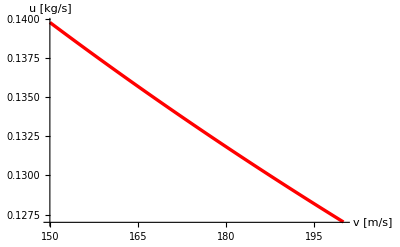

```mathematica
rys1 = Plot[u /.A /. m->2,{v,150,200},

PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","u [kg/s] "}]
```

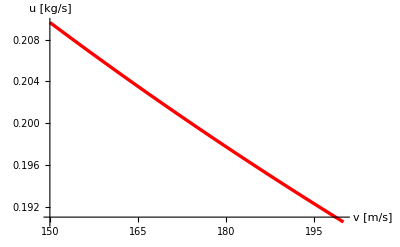

```mathematica
rys2 = Plot[u /.A /. m->3,{v,150,200},

PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","u [kg/s] "}]
```